## SimPlot-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sat 10 Nov 2012 17:35:08
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

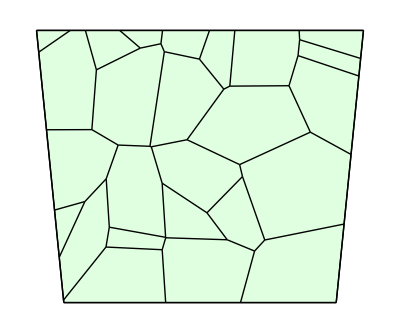

```mathematica
w=TemplateRandom[25, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
ShowTissue[w]
```

## Set up a model and run a simulation

```mathematica
n=NTissueCells[w]; 
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}, {A-> A+X, 1}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}], X[i]-> 0};
myic=Flatten[ic/@Range[n]];
```

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net,"Diffusion"-> {{A, DA}, {B,DB}}];
```

25 Cells.

5 internal reactions in each cell.

125 intracellular reactions.

216 diffusion reactions.

341 total reactions.

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,50}];
```

## Use SimPlot to plot everything

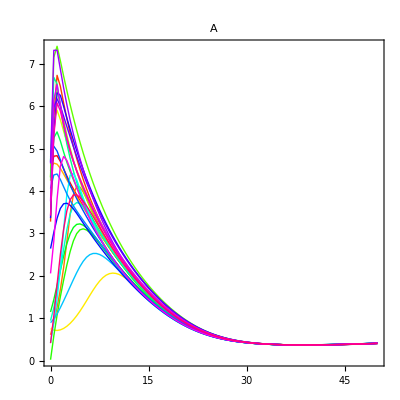
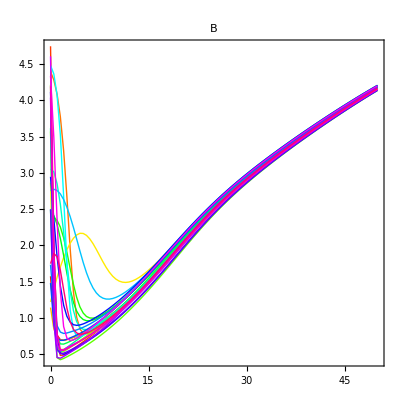
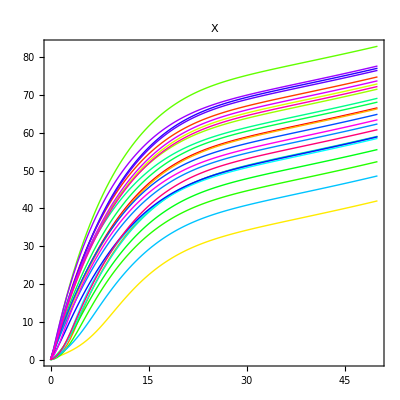

```mathematica
SimPlot[sim]
```

## Use SimPlot to plot a specific variable with specific options

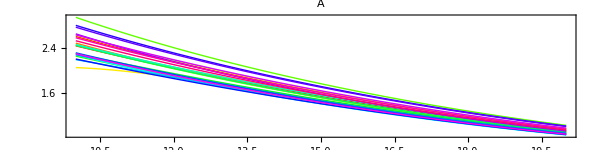

```mathematica
SimPlot[sim, A ,{10, 20}, ImageSize-> 600, AspectRatio-> 0.25, BaseStyle-> {FontSize-> 16}]
```

## Use SimPlot to Plot a specified list of variables for a specific time span

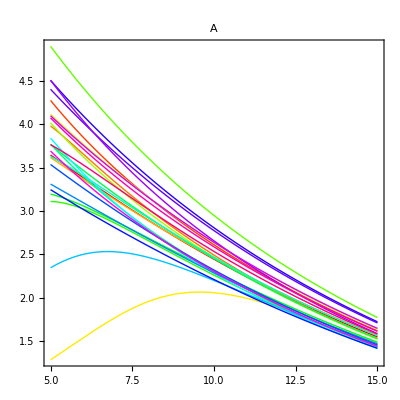
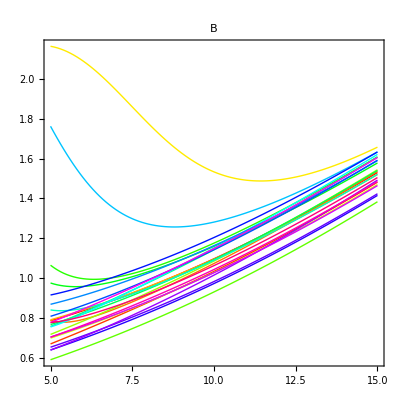

```mathematica
SimPlot[sim, {A,B}, {5, 15}]
```